## 5 - calculating linear weights

```mathematica
c1=({{1/Sqrt[2]}, {1/Sqrt[2]}})
c2=({{1/Sqrt[2]}, {-1/Sqrt[2]}})
```

{{1/(√2)},{1/(√2)}}

{{1/(√2)},{-1/(√2)}}

```mathematica
q=({{2}, {3}})
```

{{2},{3}}

## 6 - orthonormal

```mathematica
Vector[S_,Q_]:=(1/Sqrt[S])(Table[E^(I*2*Pi*Q/S(N-1)),{N,0,S-1}])
```

```mathematica
i=0;
k=1;
vi=Vector[8,i]
vk=Vector[8,k]
```

{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)}

{ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),ⅇ^((ⅈ π)/4)/(2 √2),ⅈ/(2 √2),ⅇ^((3 ⅈ π)/4)/(2 √2),-1/(2 √2),ⅇ^(-(3 ⅈ π)/4)/(2 √2),-ⅈ/(2 √2)}

```mathematica
sum=(#1+#2)&[vi,vk]
```

{1/(2 √2)+ⅇ^(-(ⅈ π)/4)/(2 √2),1/(√2),1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2),(1/2+ⅈ/2)/(√2),1/(2 √2)+ⅇ^((3 ⅈ π)/4)/(2 √2),0,1/(2 √2)+ⅇ^(-(3 ⅈ π)/4)/(2 √2),(1/2-ⅈ/2)/(√2)}

```mathematica
data=Transpose@{Re[sum],Im[sum]}
```

{{1/4+1/(2 √2),-1/4},{1/(√2),0},{1/4+1/(2 √2),1/4},{1/(2 √2),1/(2 √2)},{-1/4+1/(2 √2),1/4},{0,0},{-1/4+1/(2 √2),-1/4},{1/(2 √2),-1/(2 √2)}}

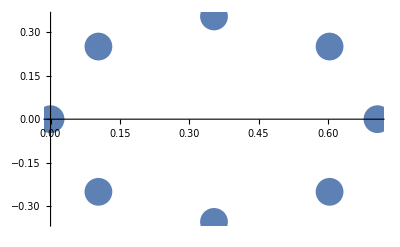

```mathematica
ListPlot[data,PlotStyle->PointSize[.05]]
```

```mathematica
N@Total[sum]
```

2.82843+0. ⅈ

```mathematica
vi=Transpose[{vi}];
vk=Transpose[{vk}];
```

```mathematica
Chop[N@ConjugateTranspose[vi].vk]
```

{{0}}

## 8 - dotting a unit vector with itself is 1

```mathematica
vector=({{1, 2, 34, 5, 6}})
```

{{1,2,34,5,6}}

```mathematica
vector=vector/Norm[vector]
```

{{1/(√1222),√(2/611),17 √(2/611),5/(√1222),3 √(2/611)}}

```mathematica
vector.Transpose@vector
```

{{1}}

## 11 - calculate the 64 point dft of a cos of frequency pi/4 radians

```mathematica
numberSamples=64;
numberRange=Range[0, numberSamples-1];
x=Cos[Pi/4 * numberRange];
DFT=FourierMatrix[numberSamples];
```

```mathematica
xDFT=DFT.x
```

{0,62,ⅇ^(-(ⅈ π)/32)/(8 √2)+ⅇ^((ⅈ π)/32)/(8 √2)-ⅇ^(-(3 ⅈ π)/32)/(8 √2)-ⅇ^((3 ⅈ π)/32)/(8 √2)-1/8 ⅇ^(-(ⅈ π)/8)-1/8 ⅇ^((ⅈ π)/8)-ⅇ^(-(5 ⅈ π)/32)/(8 √2)-ⅇ^((5 ⅈ π)/32)/(8 √2)+ⅇ^(-(7 ⅈ π)/32)/(8 √2)+ⅇ^((7 ⅈ π)/32)/(8 √2)+1/8 ⅇ^(-(ⅈ π)/4)+1/8 ⅇ^((ⅈ π)/4)+ⅇ^(-(9 ⅈ π)/32)/(8 √2)+ⅇ^((9 ⅈ π)/32)/(8 √2)-ⅇ^(-(11 ⅈ π)/32)/(8 √2)-ⅇ^((11 ⅈ π)/32)/(8 √2)-1/8 ⅇ^(-(3 ⅈ π)/8)-1/8 ⅇ^((3 ⅈ π)/8)-ⅇ^(-(13 ⅈ π)/32)/(8 √2)-ⅇ^((13 ⅈ π)/32)/(8 √2)+ⅇ^(-(15 ⅈ π)/32)/(8 √2)+ⅇ^((15 ⅈ π)/32)/(8 √2)+ⅇ^(-(17 ⅈ π)/32)/(8 √2)+ⅇ^((17 ⅈ π)/32)/(8 √2)-ⅇ^(-(19 ⅈ π)/32)/(8 √2)-ⅇ^((19 ⅈ π)/32)/(8 √2)-1/8 ⅇ^(-(5 ⅈ π)/8)-1/8 ⅇ^((5 ⅈ π)/8)-ⅇ^(-(21 ⅈ π)/32)/(8 √2)-ⅇ^((21 ⅈ π)/32)/(8 √2)+ⅇ^(-(23 ⅈ π)/32)/(8 √2)+ⅇ^((23 ⅈ π)/32)/(8 √2)+1/8 ⅇ^(-(3 ⅈ π)/4)+1/8 ⅇ^((3 ⅈ π)/4)+ⅇ^(-(25 ⅈ π)/32)/(8 √2)+ⅇ^((25 ⅈ π)/32)/(8 √2)-ⅇ^(-(27 ⅈ π)/32)/(8 √2)-ⅇ^((27 ⅈ π)/32)/(8 √2)-1/8 ⅇ^(-(7 ⅈ π)/8)-1/8 ⅇ^((7 ⅈ π)/8)-ⅇ^(-(29 ⅈ π)/32)/(8 √2)-ⅇ^((29 ⅈ π)/32)/(8 √2)+ⅇ^(-(31 ⅈ π)/32)/(8 √2)+ⅇ^((31 ⅈ π)/32)/(8 √2)}
 |  |  |  |

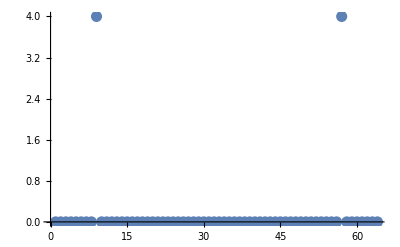

```mathematica
ListPlot[xDFT,PlotStyle->PointSize[.02]]
```

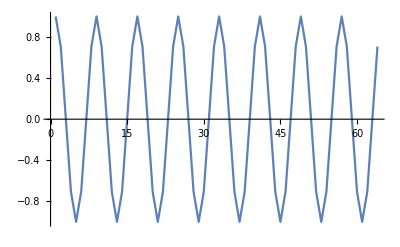

```mathematica
ListLinePlot[x]
```

## 13 - low pass using fourier and inverse fourier

```mathematica
lowpassFourierFilter[data_]:=Module[{fWeights,lWeights},
fWeights=Fourier[data];
lWeights=Join[fWeights[[;;Floor[Length[data]/4]]],.1*fWeights[[Floor[Length[data]/4]+1;;]]];Return[Re[Chop[InverseFourier[lWeights]]]]]
```

```mathematica
Fs=8192
data=Flatten[Transpose[Import["/home/nathan/olin/fall2016/QEAFall2016Homework/bset1/matlab/handel.csv"]]];
```

8192

### highest frequency

```mathematica
Fs/2
```

4096

### lowest frequency

```mathematica
0
```

0

```mathematica
dataFiltered=lowpassFourierFilter[data]
```

{-0.00538123,-0.0177226,-0.025308,-0.0160855,0.000450921,0.0183174,0.0161275,-0.00682954,-0.026557,-0.0399389,-0.0572852,-0.08448,-0.106186,-0.0919217,-0.0421564,-0.0118159,-0.0191307,-0.0312334,73077,0.0838113,0.0722977,0.0473331,0.0359092,0.0480158,0.0165222,-0.0353874,-0.0828198,-0.103739,-0.0815486,-0.0313233,0.0222903,0.0677911,0.0880384,0.0959882,0.105543,0.0756967,0.0241307}
 |  |  |  |

```mathematica
ListPlay[dataFiltered]
```

-Graphics-

## 14 - filter hum

```mathematica
guitarFs=44100;
```

```mathematica
guitarData=Import["/home/nathan/olin/fall2016/QEAFall2016Homework/bset1/matlab/guitar1_60Hz_hum.wav","Data"]
ListPlay[guitarData,SampleRate->guitarFs]
```

{-0.0154724,-0.0160522,-0.0166626,-0.0168457,-0.0168762,-0.0173645,-0.0177917,-0.0185242,-0.0195618,83773,0.0828883,0.084994,0.0780969,0.073336,0.0682699,0.0531022,0.0375683,0.0326548,0.0314951}
 |  |  |  |

-Graphics-

```mathematica
guitarDataFiltered=lowpassFourierFilter[guitarData]
ListPlay[guitarData,SampleRate->guitarFs]
```

{-0.00277813,-0.0103082,-0.0115646,-0.00897426,-0.00820755,-0.0101797,-0.0112135,-0.0102478,83775,0.0458807,0.043966,0.0404823,0.0354255,0.0286758,0.0227108,0.0181235,0.0113857}
 |  |  |  |

-Graphics-

```mathematica
data=Re[Fourier[guitarDataFiltered]]
```

{-0.192972,-0.0099005,0.00241204,-0.00854094,-0.0119331,-0.011744,-0.0153276,-0.0213279,83775,-0.0102596,-0.0213279,-0.0153276,-0.011744,-0.0119331,-0.00854094,0.00241204,-0.0099005}
 |  |  |  |

```mathematica
Length[data]
```

83791

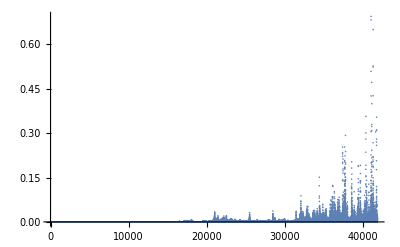

```mathematica
ListPlot[Abs@data[[Floor[83791/2];;]],PlotRange->All]
```

```mathematica
Frequency=Range[-guitarFs/2,guitarFs/2,1]
```

{-22050,-22049,-22048,-22047,-22046,-22045,-22044,-22043,-22042,-22041,-22040,-22039,-22038,-22037,-22036,-22035,-22034,-22033,-22032,-22031,-22030,-22029,-22028,-22027,-22026,-22025,-22024,-22023,44045,22023,22024,22025,22026,22027,22028,22029,22030,22031,22032,22033,22034,22035,22036,22037,22038,22039,22040,22041,22042,22043,22044,22045,22046,22047,22048,22049,22050}
 |  |  |  |